## Lab 4 - Compartmental and spatial models Looking at compartmental and spatial modeling in cellular biology and some of the difference between these two approaches. Many biological processes are happening in either different compartments or are spatially separated. The spatiotemporal dynamics of substances and their concentrations can be modeled by different mathematical frameworks, which include compartmental models (e.g. modelling organelles), reaction-diffusion equations and stochastic simulations. Compartmental modeling - an introduction A multi-compartmental model is a mathematical model used for describing how materials/energies are transported between different compartments of a system. The compartments are assumed to each be homogeneous. A second assumption is that there is fast diffusion in the compartments, and if the compartments resemble each other and rapid mixing between them would not make a difference, they can be treated as a single compartment. To make multi-compartmental modeling easier, certain assumptions can be made (that rarely exist in reality), by assuming a certain “topology” with the most known: - Closed model (sinks and sources do not exist) - Open model (sinks and sources do exist). Complex calcium oscillations To study the complex behaviour of calcium oscillations, including bursting and chaos, we develop a multi-compartmental model of intracellular calcium oscillations. The following figure schematically shows the cellular model system, including the Endoplasmic Reticulum (ER), mitochondria and calcium binding proteins (Pr) in the cytosol, which are all seen as calcium stores. -Graphics- Figure 1: Schematic representation of the model system. Includes the Endoplasmic Reticulum (ER), mitochondria and calcium binding proteins (Pr) in the cytosol. When we apply the conservation relations for total cellular calcium, the number of model variables reduces to three independent variables: -Graphics- For the total concentration of bound and unbound proteins the following equation applies: -Graphics- Next, we have three PDEs that describe the rates of change of calcium in the model: -Graphics- -Graphics- -Graphics- The fluxes of this model are given by: -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- Finally, the model parameters are shown in the following table: -Graphics-

Methods
In this section, we first identify all components of the above model and we will shortly touch upon each of them. Next. we actually build the model. We will use the parameters stated in Table 1 and use the starting positions Ca_0 = 0.3, ER Ca_0 = 0.2 and mitochondria Ca_0 = 1. After this, we plot the calcium concentrations of the different compartments over time. We also plot the cytosolic vs. mitochondrial calcium concentrations from t = 100 to t = 300.

To investigate the behaviour of this model, we change the permeability of the Ca channels to 4000 s^-1 and then 2950 s^-1 and plot the calcium concentrations again. 

Finally, we look into what would happen if the Ca channel proteins are not transcribed and translated into a function protein. We say that this might be caused by a genetic defect. We attempt to rewrite the equations in the model that it fits such a description and investigate what will happen to the system.

Results and Discussion 
The complex behaviour of calcium oscillations is studied using a multi-compartment model of intracellular calcium oscillations. Conservation relations are applied for total cellular Calcium and Calcium-binding proteins, reducing the number of independent variables to three.

When identifying all the components of the model as described in the introduction, we see that there are three compartments in this model: one for the Endoplasmic Reticulum, one for the Mitochondria and one is the Cytosol. There are two parameters for the total concentrations of Calcium and Calcium binding proteins (Pr) and they are the same the entire simulation, because the model of the cell is closed. Furthermore, we have fluxes in and out of the ER and Mitochondria.

The flux of the pump J_pump is only dependent on the Calcium concentration in the cytosol (and the value of the kinetic parameter k_pump). If the concentration in the cytosol gets higher, the flux into the ER also gets higher.

The flux of the channels is dependent on the concentration in the cytosol and on the difference in concentration between the ER and cytosol. 

The flux that leaks from the ER depends on the difference between the ER and cytosol. The higher the difference between the ER and cytosol, the more calcium leaks from the ER (if the calcium concentration in the ER is higher).

The flux that goes into the mitochondria is dependent on the concentration of calcium in the cytosol. If this concentration is high, the flux that goes into the mitochondria is also high.

The flux that goes out is dependent on both the  concentration of calcium in the cytosol and in the mitochondria itself. If the concentration in the mitochondria is high, the flux that goes out also gets higher.

We build this model in Mathematica using the parameters given in table 1 and the starting concentration of cytosolic Ca, ER Ca and mitochondria Ca 0.3, 0.3 and 1 respectively.

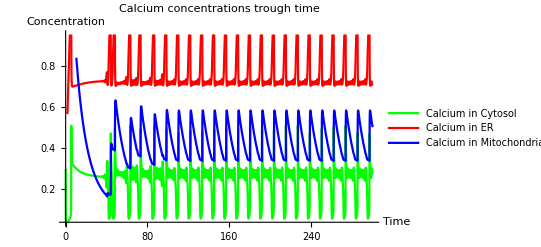

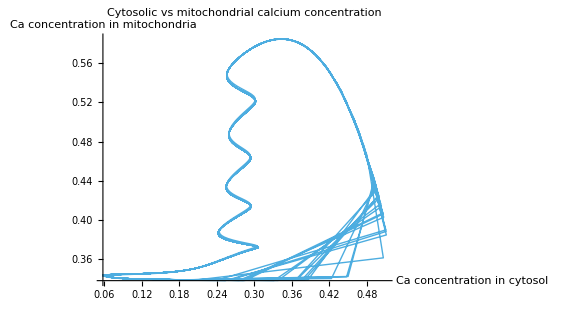

-Graphics3D-

```mathematica
ClearAll["Global`*"]

(* Define the parameters *)
params={Catot->90,Prtot->120,RhoEr->0.01,RhoM->0.01,BetaEr->0.0025,BetaM->0.0025,Kch->4100,Kpump->20,Kleak->0.05,Kin->300,Kout->125,Km->0.00625,Kplus->0.1,Kmin->0.01,K1->5,K2->0.8,K3->5};

fluxes = {Jpump[t]->  Kpump*Ca[t],
     Jch[t]->  Kch*((Ca[t]^2)/(K1^2 +Ca[t]^2))*(CaE[t]-Ca[t]),
     Jleak[t] ->  Kleak (CaE[t] - Ca[t]),
Jin[t]->  Kin*(Ca[t]^8)/(K2^8+Ca[t]^8),
Jout[t]->  ((Kout * Ca[t]^2/(K3^2+Ca[t]^2)) + Km)* CaM[t]};

eqs={Ca'[t] == Jch[t] + Jleak[t] - Jpump[t] + Jout[t] - Jin[t] +Kmin*CaPr[t]-Kplus*Ca[t]*Pr[t],
CaE'[t] == BetaEr *(Jpump[t] - Jch[t] - Jleak[t])/RhoEr,
CaM'[t]== BetaM*(Jin[t] -Jout[t])/RhoM,
CaPr[t]== Catot - Ca[t] - RhoEr * CaE[t] / BetaEr - RhoM * CaM[t]/BetaM,
Pr[t] == Prtot - CaPr[t],
Ca[0] == 0.3, 
CaE[0] == 0.2, 
CaM[0] == 1};

sol = NDSolve[eqs /. fluxes /. params,
{Ca[t], CaE[t], CaM[t], CaPr[t], Pr[t]}, 
{t, 0, 300}];

pltCacy = Plot[Ca[t] /. sol,{t,00,300}, PlotStyle->Green, PlotLegends->{"Calcium in Cytosol"}];
pltCaEr = Plot[CaE[t] /. sol,{t,00,300}, PlotStyle->Red, PlotLegends->{"Calcium in ER"}];
pltCaMyto = Plot[CaM[t] /. sol,{t,00,300}, PlotStyle->Blue, PlotLegends->{"Calcium in Mitochondrial"}];
Show[{pltCacy, pltCaEr, pltCaMyto}, PlotRange->All, AxesLabel-> {"Time", "Concentration"}, PlotLabel-> "Calcium concentrations trough time"]

ParametricPlot[{Ca[t] , CaM[t]}/.sol, {t,100,300},ImageSize-> Large,  PlotLabel-> "Cytosolic vs mitochondrial calcium concentration", AxesLabel->{"Ca concentration in cytosol", "Ca concentration in mitochondria"}, PlotTheme->"PastelColor"]

ParametricPlot3D[{Ca[t], CaM[t], CaE[t]}/.sol, {t, 100, 300}, ImageSize->Large, PlotLabel-> "Cytosolic vs mitochondrial vs ER calcium concentration", AxesLabel->{"Ca concentration in cytosol", "Ca concentration in mitochondria", "Ca concentration in ER"}, PlotTheme->"PastelColor"]
```

First, we see that the concentration of Calcium in the Mitochondria goes down quite a bit from 0.85 to 0.2, and after 50 timesteps we note that the intracellular calcium oscillations seem to stabilize into the same pattern. 

Next, we change the maximal permeability of the Ca channels to 4000 s^-1 and then 2950 s^-1.

```mathematica
(* Define the parameters*)
params={Catot->90,Prtot->120,RhoEr->0.01,RhoM->0.01,BetaEr->0.0025,BetaM->0.0025,Kch->4000,Kpump->20,Kleak->0.05,Kin->300,Kout->125,Km->0.00625,Kplus->0.1,Kmin->0.01,K1->5,K2->0.8,K3->5};

sol4000 = NDSolve[eqs /. fluxes/. params,
{Ca[t], CaE[t], CaM[t]}, 
{t, 0, 300}];

pltCacy = Plot[Ca[t] /. sol4000,{t,00,300}, PlotStyle->Green, PlotLegends->{"Ca Cytosol"}];
pltCaEr = Plot[CaE[t] /. sol4000,{t,00,300}, PlotStyle->Red, PlotLegends->{"Ca ER"}];
pltCaMyto = Plot[CaM[t] /. sol4000,{t,00,300}, PlotStyle->Blue, PlotLegends->{"Ca Mitochondrial"}];

CaConcs1 = Show[{pltCacy, pltCaEr, pltCaMyto}, PlotRange->All, ImageSize->Medium, AxesLabel-> {"Time", "Concentration"}, PlotLabel-> "Calcium concentrations trough time" ];

params={Catot->90,Prtot->120,RhoEr->0.01,RhoM->0.01,BetaEr->0.0025,BetaM->0.0025,Kch->2950,Kpump->20,Kleak->0.05,Kin->300,Kout->125,Km->0.00625,Kplus->0.1,Kmin->0.01,K1->5,K2->0.8,K3->5};

sol2950 = NDSolve[eqs/. fluxes /. params,
{Ca[t], CaE[t], CaM[t]}, 
{t, 0, 300}];

pltCacy = Plot[Ca[t] /. sol2950,{t,00,300}, PlotStyle->Green, PlotLegends->{"Ca Cytosol"}];
pltCaEr = Plot[CaE[t] /. sol2950,{t,00,300}, PlotStyle->Red, PlotLegends->{"Ca ER"}];
pltCaMyto = Plot[CaM[t] /. sol2950,{t,00,300}, PlotStyle->Blue, PlotLegends->{"Ca Mitochondrial"}];

CaConcs2 = Show[{pltCacy, pltCaEr, pltCaMyto}, PlotRange->All, ImageSize->Medium, AxesLabel-> {"Time", "Concentration"}, PlotLabel-> "Calcium concentrations trough time"];

pp1 = ParametricPlot[{Ca[t] , CaM[t]}/.sol4000, {t,100,300},ImageSize-> Large,  PlotLabel-> "Cytosolic vs mitochondrial calcium concentration", AxesLabel->{"Ca concentration in cytosol", "Ca concentration in mitochondria"}, PlotTheme->"PastelColor"];

pp2 = ParametricPlot[{Ca[t] , CaM[t]}/.sol2950, {t,100,300},ImageSize-> Large,  PlotLabel-> "Cytosolic vs mitochondrial calcium concentration", AxesLabel->{"Ca concentration in cytosol", "Ca concentration in mitochondria"}, PlotTheme->"PastelColor"];

GraphicsGrid[{{CaConcs1, CaConcs2}}]
```

-Graphics-

The Channel permeability, K_ch, was 4100 s^-1 and when we lower it to 4000 s^-1 the difference (that we can see by eye in this graph) is that the Calcium concentration in the mitochondria doesn’t go to the same oscillating state as in the previous plot. There seems to be a pattern, but it is a different, longer pattern. When we lowered it even more, to 2950 s^-1, we also see that the concentration of Ca in the mitochondria goes up a lot. In this plot, we don’t really see an equilibration time. It looks like there is a stable pattern, but around 175 and 275 timesteps there are some varieties.

To investigate these two systems even more, we plotted the cytosolic versus the mitochondrial calcium concentrations, just like in the previous system.

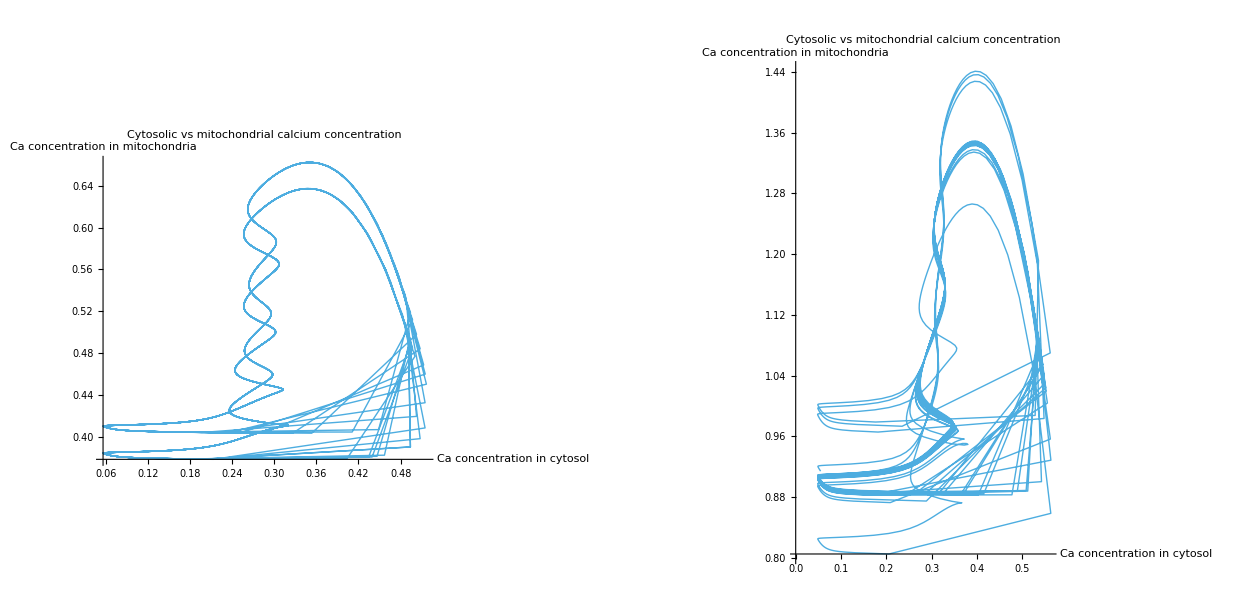

```mathematica
GraphicsGrid[{{pp1, pp2}}]
```

We see here that 

Finally, we assume that the Ca channel proteins are not transcribed and translated into a functional protein, due to a genetic mutation. The equations of the model are rewritten with a flux J_channel of zero. The Calcium concentration in the ER will rise, because the Calcium can’t escape trough the channels anymore, and the speed at which it leaves the ER thus goes down. For the oscillating behavior we think these channels are needed. We won’t see any more oscillations. To see if these thoughts are right, the model with K_ch= 0 has been plotted.

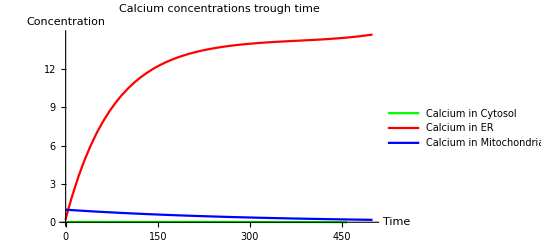

```mathematica
ClearAll["Global`*"]

(* Define the parameters*)
params={Catot->90,Prtot->120,RhoEr->0.01,RhoM->0.01,BetaEr->0.0025,BetaM->0.0025,Kch->0,Kpump->20,Kleak->0.05,Kin->300,Kout->125,Km->0.00625,Kplus->0.1,Kmin->0.01,K1->5,K2->0.8,K3->5};

fluxes = {Jpump[t]->  Kpump*Ca[t],
     Jch[t]->  0,
     Jleak[t] ->  Kleak (CaE[t] - Ca[t]),
Jin[t]->  Kin*(Ca[t]^8)/(K2^8+Ca[t]^8),
Jout[t]->  ((Kout * Ca[t]^2/(K3^2+Ca[t]^2)) + Km)* CaM[t]};

eqs={Ca'[t] == Jleak[t] - Jpump[t] + Jout[t] - Jin[t] +Kmin*CaPr[t]-Kplus*Ca[t]*Pr[t],
CaE'[t] == BetaEr *(Jpump[t] - Jch[t] - Jleak[t])/RhoEr,
CaM'[t]== BetaM*(Jin[t] -Jout[t])/RhoM,
CaPr[t]== Catot - Ca[t] - RhoEr * CaE[t] / BetaEr - RhoM * CaM[t]/BetaM,
Pr[t] == Prtot - CaPr[t],
Ca[0] == 0.3, 
CaE[0] == 0.2, 
CaM[0] == 1};

solNoPr = NDSolve[eqs /. fluxes /. params,
{Ca[t], CaE[t], CaM[t], CaPr[t], Pr[t]}, 
{t, 0, 300}];

pltCacy = Plot[Ca[t] /. solNoPr,{t,0,500}, PlotStyle->Green, PlotLegends->{"Calcium in Cytosol"}];
pltCaEr = Plot[CaE[t] /. solNoPr,{t,0,500}, PlotStyle->Red, PlotLegends->{"Calcium in ER"}];
pltCaMyto = Plot[CaM[t] /. solNoPr,{t,0,500}, PlotStyle->Blue, PlotLegends->{"Calcium in Mitochondrial"}];

Show[{pltCacy, pltCaEr, pltCaMyto}, PlotRange->All, AxesLabel-> {"Time", "Concentration"}, PlotLabel-> "Calcium concentrations trough time"]
```

We see that the calcium concentration in the ER indeed goes up.

Conclusions

# Reaction-Diffusion systems

A reaction diffusion system is a system that describes several substances that diffuse and participate in reactions. The system is obtained by combining a kinetic model for chemical reactions and the diffusion equation. A reaction -diffusion system can be used to, for example, show the spread of pigmentation in animals. In this way, it can be used to explain how patterns are formed. 

The general reaction-diffusion equation is given by:
(∂u)/(∂t)=D_u∇^2 u+f(u)

Here, D_u is the diffusion constant of u and f(u) the function describing the reaction kinetics of u.

The idea is that patterns can form from systems that have a homogeneous steady state. The steady state must be unstable against spatial variation (i.e. diffusion) but stable against homogeneous concentration changes. Such a system can easily be modelled using an activator u and an inhibitor v. In order to form patterns, the inhibitor must defuse faster than the activator in order to enclose the activator. The activator can then activate for example pigment, after which a pattern is formed. 
-Graphics-
Figure 2: Activator and inhibitor graph.

In this section, we take a look at the Gierer-Meinhardt system. This system is a system that can describe pattern formation as described above. 

In order to guarantee a unique solution, some boundary conditions are needed. The most commonly used conditions are the Neumann boundary and initial conditions. For a one-dimensional homogeneous system. these conditions are the following:

	u_x(0,t)=u_x(1,t)= v_x(0,t)= v_x(1,t)= 0
u(x,0)=u_0(x)
v(x,0)=v_0(x)

Methods
In this section, systems for pattern formation are investigated. First we take a look at the Gierer-Meinhardt system in two-dimensional space. The complete set of reaction-diffusion equations and boundary conditions are found, and this model is then solved. The parameters for the specific equations are the ones found in the table below.

```mathematica
Grid[{{"D_u = ϵ = 0.0004",
"D_v = d = 0.04"},
{"p = 2",
"q = 1"},
{"r = 2",
"s = 0"},
{"x_0 = 0",
"x_1 = 5"},
{"y_0 = 0",
"y_1 = 5"},
{"t_0 = 0",
"t_1 = 500"},
{"u_0 = 1",
"v_0 = 2"}}]
```

D_u = ϵ = 0.0004 | D_v = d = 0.04
p = 2 | q = 1
r = 2 | s = 0
x_0 = 0 | x_1 = 5
y_0 = 0 | y_1 = 5
t_0 = 0 | t_1 = 500
u_0 = 1 | v_0 = 2

Next, the u and v patterns are plotted using a density plot. 

Next, we take a look what will happen if we combine the Gierer-Meinhardt model with another type of kinetics: the Schnakenberg model. This model is an example of an activator-substrate system where a fast diffusing substrate v is consumed by a slow diffusing activator u.

The kinetics are given by: 

 	f(u,v)=c_1-c_-1 u + c_3 u^2 v
g(u,v) =c_2-c_3 u^2 v 

We solve this model once again in 2-D with the periodic boundary conditions (x_0 = x_n), on a 100 x 100 space for 1000 time units. The parameters used are:

```mathematica
Grid[{{"D_u = ϵ = 0.0004",
"D_v = d = 0.016"},
{"x_0 = 0",
"x_1 = 100"},
{"y_0 = 0",
"y_1 = 100"},
{"t_0 = 0",
"t_1 = 1000"},
{"u_0 = 1",
"v_0 = 3"},
{"c_1 = 0.1",
"c_2 = 0.9"},
{"c_-1 = 1",
"c_3 = 1"}}]
```

D_u = ϵ = 0.0004 | D_v = d = 0.016
x_0 = 0 | x_1 = 100
y_0 = 0 | y_1 = 100
t_0 = 0 | t_1 = 1000
u_0 = 1 | v_0 = 3
c_1 = 0.1 | c_2 = 0.9
c_-1 = 1 | c_3 = 1

Results and Discussion
The complete set of reaction-diffusion equations and boundary conditions of the Gierer-Meinhardt system in two-dimensional space are derived from the equations of the one-dimensional system.

Reaction diffusion equations:
(∂u)/(∂t)=D_u( (∂^2 u)/(∂x^2) + (∂^2 u)/(∂y^2))u-u +u^p/v^q

(∂v)/(∂t)=D_v( (∂^2 v)/(∂x^2) + (∂^2 v)/(∂y^2))v-v +u^r/v^s

Boundary conditions:
u_x(0, 0,t)= u_x(0, 1,t) = u_x(1, 0,t)=u_x(1, 1,t)= 0
v_x(0,0,t) = v_x(0,1,t) =v_x(1,0,t)= v_x(1,1,t)= 0
u(x,y, 0)=u_0(x, y)
v(x,y,0)=v_0(x,y)

The above model is solved with the parameters stated above. The solved model is plotted below.

```mathematica
ClearAll["Global`*"]

(*define the equations and Neuman boundary conditions (closed)*)
eqsGierer = {D[u[t,x, y],t] == -u[t,x, y] + u[t,x, y]^p/v[t,x, y]^q+ϵ D[u[t,x, y],x,x] + ϵ D[u[t,x, y],y,y], 
D[v[t,x, y],t]==-v[t,x, y]+u[t,x, y]^r/v[t,x, y]^s+d D[v[t,x, y],x,x] + d D[v[t,x,y],y,y],
Derivative[0,1, 0][u][t,x0, y]==0,
Derivative[0,1, 0][u][t,x1, y]==0,
Derivative[0,1, 0][v][t,x0, y]==0,
Derivative[0,1, 0][v][t,x1, y]==0,
Derivative[0,0, 1][u][t,x, y0]==0,
Derivative[0,0, 1][u][t,x, y1]==0,
Derivative[0,0, 1][v][t,x, y0]==0,
Derivative[0,0, 1][v][t,x, y1]==0,
u[t0,x, y]==u0,
v[t0,x, y]==v0};

(*define the parameters*)
paramsGierer = {p->2, q->1, r-> 2, s->0, ϵ -> 0.0004, d-> 0.04, x0->0, x1->5, y0-> 0, y1-> 5, t0-> 0, t1-> 500, u0-> 1, v0-> 2};

(*solve the system*)
solGierer=NDSolve[eqsGierer/.paramsGierer,{u, v}, {t, t0,t1 }/.paramsGierer, {x, x0,x1 }/.paramsGierer, {y, y0, y1}/.paramsGierer,PrecisionGoal->1]

Manipulate[DensityPlot[{u[t, x, y]/.solGierer},{x, x0,x1}/.paramsGierer,{y,y0,y1}/.paramsGierer,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->All,PerformanceGoal->"Quality", PlotLabel->"Concentrations of activator u", FrameLabel->{"x", "y"}],{{t, 50}, 0, 500, Appearance->"Labeled"}]

Manipulate[DensityPlot[{v[t, x, y]/.solGierer},{x, x0,x1}/.paramsGierer,{y,y0,y1}/.paramsGierer,PlotLegends->Automatic,PlotRange->All,
PerformanceGoal->"Quality", ColorFunction->"Rainbow", PlotLabel->"Concentrations of inhibitor v", FrameLabel->{"x", "y"}],{{t, 50}, 0, 500, Appearance->"Labeled"}]
```

{{u→InterpolatingFunction[{{0., 500.}, {0., 5.}, {0., 5.}}, <>],v→InterpolatingFunction[{{0., 500.}, {0., 5.}, {0., 5.}}, <>]}}

The plots show where the u and v are the most present. Over time, the concentration changes. In the beginning, both u and v are distributed equally over the whole plane. Over time, the concentrations will increase in some areas and decrease in others, resulting in patterns. These patterns continue to evolve over time, but they appear to stabilise around t = 100. 

Next, the Gierer-Meinhardt model is swapped with another type of kinetics, the Schnakenberg model. The reaction diffusion equations become:
(∂u)/(∂t)=D_u( (∂^2 u)/(∂x^2) + (∂^2 u)/(∂y^2))u+ c_1-c_-1 u + c_3 u^2 v

(∂v)/(∂t)=D_v( (∂^2 v)/(∂x^2) + (∂^2 v)/(∂y^2))v+ c_2-c_3 u^2 v 

The boundary conditions for this model stay the same. The model is solved and the resulting plots can be found below.

```mathematica
paramsSchnaken = {Du-> 0.0004, ϵ-> 0.0004, Dv -> 0.016, d -> 0.016, u0-> 1, v0-> 3, c1-> 0.1, c2-> 0.9, c1m-> 1, c3-> 1, x0-> 0, x1-> 100, y0-> 0,y1-> 100, t0-> 0, t1-> 1000}

eqsSchnaken={D[u[t,x,y],t]==c1-c1m*u[t,x,y]+c3*u[t,x,y]^2*v[t,x,y]+ϵ D[u[t,x,y],x,x]+ϵ D[u[t,x,y],y,y],D[v[t,x,y],t]==c2-c3*u[t,x,y]^2*v[t,x,y]+d D[v[t,x,y],x,x]+d D[v[t,x,y],y,y],
Derivative[0,1,0][u][t,x0,y]==Derivative[0,1,0][u][t,x1,y],
Derivative[0,1,0][v][t,x0,y]==Derivative[0,1,0][v][t,x1,y],
Derivative[0,0,1][u][t,x,y0]==Derivative[0,0,1][u][t,x,y1],
Derivative[0,0,1][v][t,x,y0]==Derivative[0,0,1][v][t,x,y1],
u[t0,x,y]==u0,
v[t0,x,y]==v0};

solSchnaken=NDSolve[eqsSchnaken/.paramsSchnaken,{u,v},{t,t0,t1}/.paramsSchnaken,{x,x0,x1}/.paramsSchnaken,{y,y0,y1}/.paramsSchnaken,PrecisionGoal->1];

uConc = Manipulate[DensityPlot[{u[t, x, y]/.solSchnaken},{x, x0,x1}/.paramsSchnaken,{y,y0,y1}/.paramsSchnaken,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->All,PerformanceGoal->"Quality", PlotLabel->"Concentrations of activator u", FrameLabel->{"x", "y"}],{{t, 200}, 0, 1000, Appearance->"Labeled"}]

vConc = Manipulate[DensityPlot[{v[t, x, y]/.solSchnaken},{x, x0,x1}/.paramsSchnaken,{y,y0,y1}/.paramsSchnaken,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->All,PerformanceGoal->"Quality", PlotLabel->"Concentrations of inhibitor v", FrameLabel->{"x", "y"}],{{t, 200}, 0, 1000, Appearance->"Labeled"}]
```

{Du→0.0004,ϵ→0.0004,Dv→0.016,d→0.016,u0→1,v0→3,c1→0.1,c2→0.9,c1m→1,c3→1,x0→0,x1→100,y0→0,y1→100,t0→0,t1→1000}

The above plots clearly show that the concentration of u is the inverse of the concentration of v. This was not visible in the plot of the Gierer-Meinhardt model. In the model with the Schnakenberg kinetics, the concentrations once again start out evenly distributed over the plains. They soon begin to change and distribute themselves over the whole plane. However, unlike with the Gierer-Meinhardt model, here the concentrations go back to being evenly distributed over the whole plane. This happens around t = 675. However, soon after that they seem to gather more in some places again before the plot once again shows an even distribution around t = 745.  

Conclusions
From the above results we can conclude that the Gierer-Meinhardt model is very hard to solve analytically. We do not get the patterns we would expect to see based on this information.